```mathematica
ClearAll["Global`*"];
```

```mathematica
coords = {t,r,θ,ϕ};
n=Length[coords];
rplus = M+Sqrt[M^2-a^2];
tt=2 M r/ρ-1;
rr=ρ/Δ;
θθ=ρ;
ϕϕ=(Δ+(2 M r (r^2+a^2))/ρ)Sin[θ]^2;
tϕ=-4 a M r Sin[θ]^2/ρ;
metric={{tt,0,0,tϕ},{0,rr,0,0},{0,0,θθ,0},{tϕ,0,0,ϕϕ}};
metric//MatrixForm;
inversemetric=Simplify[Inverse[metric]];
inversemetric //MatrixForm;
```

```mathematica
a=.;M=.;
ρ=r^2+a^2 Cos[θ]^2;
Δ=r^2 - 2 M r+ a^2;
christoffel:=christoffel=Simplify[Table[(1/2)*Sum[(inversemetric[[i,s]])*
(D[metric[[s,j]],coords[[k]] ]+
D[metric[[s,k]],coords[[j]] ]-D[metric[[j,k]],coords[[s]] ]),{s,1,n}],
{i,1,n},{j,1,n},{k,1,n}] ]
listchristoffel:=Table[If[UnsameQ[christoffel[[i,j,k]],0],{ToString[Γ[i,j,k]],christoffel[[i,j,k]]}] ,{i,1,n},{j,1,n},{k,1,j}]
geodesic:=geodesic=Simplify[Table[-Sum[christoffel[[i,j,k]]coords[[j]]' coords[[k]]',{j,1,n},
{k,1,n}],{i,1,n}]]
listgeodesic:=Table[{"d/dτ"ToString[coords[[i]]'],"=",geodesic[[i]]},{i,1,n}]
geodesic:=geodesic=Simplify[Table[-Sum[christoffel[[i,j,k]]coords[[j]]' coords[[k]]',{j,1,n},
{k,1,n}],{i,1,n}]]
```

```mathematica
M=.;a=.;
TableForm[Partition[DeleteCases[Flatten[listchristoffel],Null],2],TableSpacing->{2,2}];
TableForm[Partition[DeleteCases[Flatten[listgeodesic],Null],2],TableSpacing->{2,2}];
christoffel[[2,1,1]]
christoffel[[2,1,1]] /. r-> 4 /. θ -> π/4
christoffel[[2,2,2]]  /. r-> 4 /. θ -> π/4
```

-(M (a^2+r (-2 M+r)) (-r^2+a^2 Cos[θ]^2))/((r^2+a^2 Cos[θ]^2)^3)

-((-16+a^2/2) (a^2+4 (4-2 M)) M)/((16+a^2/2)^3)

(4 (a^2-4 M)+1/2 a^2 (-4+M))/((16+a^2/2) (a^2+4 (4-2 M)))

```mathematica
M=1;a=0.5;
Nchristoffel = Table[Table[{r,θ,christoffel[[i,j,k]]},{r,rplus,15},{θ,0.01,π/2,0.1}],{i,1,n},{j,1,n},{k,1,n}];
```

```mathematica
Nchristoffel[[2,1,1]];
iNchristoffel = Table[Interpolation[Flatten[Nchristoffel[[i,j,k]],1],InterpolationOrder -> 3],{i,1,n},{j,1,n},{k,1,n}];
```

```mathematica
iNchristoffel[[2,1,1]][4,π/4]
christoffel[[2,1,1]] /. r-> 4 /. θ -> π/4
```

0.0313308

0.0312369

```mathematica
christoffel = iNchristoffel;
```

```mathematica
(* the solver function. It takes in the max τ, the initial velocities in r,θ,ϕ and the initial coordinates in t,r,θ,ϕ. *)
computeSoln[maxτi_,ivsi_,icsi_]:=Block[{ivs,ics,i,χ,tmp,soln},
ics=icsi;
ivs=Join[{χ},ivsi];
tmp=metric;
tmp=tmp/.Table[coords[[i]]->ics[[i]],{i,0,n}];
tmp=ivs.(tmp.ivs);
τend = maxτi;
χslv=Solve[tmp==uinvar,χ];
ivs[[1]]=Last[χ/.χslv];
deq=Table[coords[[i]]''[τ]==(geodesic[[i]]/.Join[Table[coords[[i]]'->coords[[i]]'[τ],{i,1,n}],Table[coords[[i]]->coords[[i]][τ],{i,1,n}]]),{i,1,n}];
deq=Join[deq,Table[coords[[i]]'[0]==ivs[[i]],{i,1,n}],Table[coords[[i]][0]==ics[[i]],{i,1,n}]];
soln=NDSolve[deq,coords,
{τ,0,maxτi},
Method->{"EventLocator","Event":>(r[τ]≤1.005*rplus),"EventAction":>Throw[τend=τ,"StopIntegration"]}
];
soln]
(* this next function translates from spherical coordinates to Cartesian coordinates to make plotting simpler *)
sphslnToCartsln[soln_]:=Block[{xs,ys,zs},xs=r[τ] Sin[θ[τ]] Cos[ϕ[τ]]/.soln ;ys=r[τ] Sin[θ[τ]] Sin[ϕ[τ]]/.soln;zs=r[τ] Cos[θ[τ]]/.soln;{xs,ys,zs}]
(* This one calculates u dot u *)
udotu[solni_,τval_]:=Block[{xα,uα},xα=Table[coords[[i]][τ]/.solni,{i,1,n}]//Flatten; uα=D[xα,τ];
xα=xα/.τ->τval;uα=uα/.τ->τval;uα.((metric/.Table[coords[[i]]->xα[[i]],{i,1,n}]).uα)]
(* And this one prints out the coordinates *)
coordlist[τin_,soln_]:=Table[ToString[coords[[i]]]<>" = "<>{ToString[coords[[i]][τin]/.soln//First]},{i,1,n}]
```

```mathematica
(* Define various plotting functions *)
genXYPlot[mτ_,icsin_,ivsin_,hue_]:=Block[{xyz},
soln = computeSoln[mτ,ivsin,icsin];
xyz=sphslnToCartsln[soln];
If[mτ==τend,Print["The particle did not cross the horizon for initial coordinates=",icsin," and initial velocities=",ivsin],Print["For initial coordinates=",icsin," and initial velocities=",ivsin," the particle crosses the horizon at τend=",τend]];
Print["With final coordinates=",coordlist[τend,soln]];
ParametricPlot[Evaluate[{xyz[[1]],xyz[[2]]}//Flatten],{τ,0,τend},AxesLabel->{x,y},DisplayFunction->Identity,PlotRange->All,PlotStyle->Hue[hue]]]
genXZPlot[mτ_,icsin_,ivsin_,hue_]:=Block[{xyz},
soln = computeSoln[mτ,ivsin,icsin];
xyz=sphslnToCartsln[soln];
If[mτ==τend,Print["The particle did not cross the horizon for initial coordinates=",icsin," and initial velocities=",ivsin],Print["For initial coordinates=",icsin," and initial velocities=",ivsin," the particle crosses the horizon at τend=",τend]];
Print["With final coordinates=",coordlist[τend,soln]];
ParametricPlot[Evaluate[{xyz[[1]],xyz[[3]]}//Flatten],{τ,0,τend},AxesLabel->{x,z},DisplayFunction->Identity,PlotRange->All,PlotStyle->Hue[hue]]]
genYZPlot[mτ_,icsin_,ivsin_,hue_]:=Block[{xyz},
soln = computeSoln[mτ,ivsin,icsin];
xyz=sphslnToCartsln[soln];
If[mτ==τend,Print["The particle did not cross the horizon for initial coordinates=",icsin," and initial velocities=",ivsin],Print["For initial coordinates=",icsin," and initial velocities=",ivsin," the particle crosses the horizon at τend=",τend]];
Print["With final coordinates=",coordlist[τend,soln]];
ParametricPlot[Evaluate[{xyz[[2]],xyz[[3]]}//Flatten],{τ,0,τend},AxesLabel->{y,z},DisplayFunction->Identity,PlotRange->All,PlotStyle->Hue[hue]]]
genXYZPlot[mτ_,icsin_,ivsin_,hue_]:=Block[{xyz},
soln = computeSoln[mτ,ivsin,icsin];
xyz=sphslnToCartsln[soln];
If[mτ==τend,Print["The particle did not cross the horizon for initial coordinates=",icsin," and initial velocities=",ivsin],Print["For initial coordinates=",icsin," and initial velocities=",ivsin," the particle crosses the horizon at τend=",τend]];
Print["With final coordinates=",coordlist[τend,soln]];
ParametricPlot3D[Evaluate[Re[xyz]//Flatten],{τ,0,τend},AxesLabel->{x,y,z},DisplayFunction->Identity,PlotRange->All,PlotStyle->Hue[hue]]]
```

For initial coordinates={0,12,π/2,0} and initial velocities={-0.15,0,-0.0093} the particle crosses the horizon at τend=110.784

With final coordinates={t = 42.2341,r = 1.005,θ = 1.5708,ϕ = -1.25277}

For initial coordinates={0,12,π/2,0} and initial velocities={-0.15,0,-0.0083} the particle crosses the horizon at τend=92.3315

With final coordinates={t = 33.6005,r = 1.005,θ = 1.5708,ϕ = -0.122335}

For initial coordinates={0,12,π/2,0} and initial velocities={-0.15,0,-0.0073} the particle crosses the horizon at τend=86.3085

With final coordinates={t = 29.9038,r = 1.005,θ = 1.5708,ϕ = 0.40589}

For initial coordinates={0,12,π/2,0} and initial velocities={-0.15,0,-0.0063} the particle crosses the horizon at τend=83.6191

With final coordinates={t = 27.4601,r = 1.005,θ = 1.5708,ϕ = 0.792321}

For initial coordinates={0,12,π/2,0} and initial velocities={-0.15,0,-0.0053} the particle crosses the horizon at τend=82.7443

With final coordinates={t = 25.6132,r = 1.005,θ = 1.5708,ϕ = 1.1226}

For initial coordinates={0,12,π/2,0} and initial velocities={-0.15,0,-0.0043} the particle crosses the horizon at τend=83.2493

With final coordinates={t = 24.1216,r = 1.005,θ = 1.5708,ϕ = 1.4333}

For initial coordinates={0,12,π/2,0} and initial velocities={-0.15,0,-0.0033} the particle crosses the horizon at τend=85.1153

With final coordinates={t = 22.8693,r = 1.005,θ = 1.5708,ϕ = 1.75009}

For initial coordinates={0,12,π/2,0} and initial velocities={-0.15,0,-0.0023} the particle crosses the horizon at τend=88.6809

With final coordinates={t = 21.7931,r = 1.005,θ = 1.5708,ϕ = 2.10253}

For initial coordinates={0,12,π/2,0} and initial velocities={-0.15,0,-0.0013} the particle crosses the horizon at τend=94.956

With final coordinates={t = 20.8602,r = 1.005,θ = 1.5708,ϕ = 2.54454}

For initial coordinates={0,12,π/2,0} and initial velocities={-0.15,0,-0.0003} the particle crosses the horizon at τend=107.269

With final coordinates={t = 20.0843,r = 1.005,θ = 1.5708,ϕ = 3.23237}

For initial coordinates={0,12,π/2,0} and initial velocities={-0.15,0,0.0007} the particle crosses the horizon at τend=152.399

With final coordinates={t = 19.9526,r = 1.005,θ = 1.5708,ϕ = 5.38911}

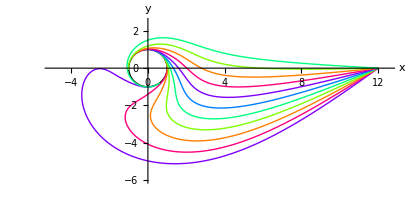

```mathematica
τend=.;uinvar = 0;
M=1;a=1;rplus=M+Sqrt[M^2-a^2];
horizpl=PolarPlot[rplus,{θ,0,2 Pi},DisplayFunction->Identity,PlotStyle->{Black,Thick}];
τPlot=200;
Table[genXYPlot[τPlot,{0,12,π/2,0},{-0.15,0,0+i*0.001},1-i*(5/6)],{i,-9.3,1.3,1}];
(*Manipulate[Show[horizpl,%,DisplayFunction->$DisplayFunction,AxesLabel->{x,y},PlotRange -> {{-coordMax,coordMax},{-coordMax,coordMax}}],{coordMax,2,10}]*)
Show[horizpl,%,DisplayFunction->$DisplayFunction,AxesLabel->{x,y},PlotRange -> {{-5,12.5},{-6,2.5}}]
```

```mathematica
τend=.;uinvar = 0;
M=1;a=0.9;rplus=M+Sqrt[M^2-a^2];
horizpl=SphericalPlot3D[{rplus,EdgeForm[]},{θ,0,Pi},{ϕ,0, 2Pi},DisplayFunction->Identity,PlotPoints->50];
τPlot = 300;
Table[genXYZPlot[τPlot,{0,10,π/3,0},{-0.05,0.001,0+i*0.001},1-i*(5/6)],{i,-2,2,1}];
Show[%,horizpl]
```

For initial coordinates={0,10,π/3,0} and initial velocities={-0.05,0.001,-0.002} the particle crosses the horizon at τend=176.881

With final coordinates={t = 30.0051,r = 1.44307,θ = 3.05105,ϕ = 1.50201}

For initial coordinates={0,10,π/3,0} and initial velocities={-0.05,0.001,-0.001} the particle crosses the horizon at τend=182.091

With final coordinates={t = 27.0749,r = 1.44307,θ = 2.988,ϕ = 2.08553}

For initial coordinates={0,10,π/3,0} and initial velocities={-0.05,0.001,0.} the particle crosses the horizon at τend=202.144

With final coordinates={t = 24.8536,r = 1.44307,θ = 2.75793,ϕ = 2.52907}

The particle did not cross the horizon for initial coordinates={0,10,π/3,0} and initial velocities={-0.05,0.001,0.001}

With final coordinates={t = 26.8032,r = 4.98672,θ = 2.0335,ϕ = 6.20278}

The particle did not cross the horizon for initial coordinates={0,10,π/3,0} and initial velocities={-0.05,0.001,0.002}

With final coordinates={t = 23.6272,r = 6.51687,θ = 2.33893,ϕ = 3.63639}

-Graphics3D-

The particle did not cross the horizon for initial coordinates={0,12,π/2,0} and initial velocities={-0.15,0,-0.0097}

With final coordinates={t = 210.381,r = 159.649,θ = 1.5708,ϕ = -6.06655}

For initial coordinates={0,12,π/2,0} and initial velocities={-0.15,0,-0.0096} the particle crosses the horizon at τend=141.954

With final coordinates={t = 55.0804,r = 1.005,θ = 1.5708,ϕ = -2.86464}

The particle did not cross the horizon for initial coordinates={0,12,π/2,0} and initial velocities={-0.15,0,0.001}

With final coordinates={t = 136.093,r = 102.414,θ = 1.5708,ϕ = 15.3562}

For initial coordinates={0,12,π/2,0} and initial velocities={-0.15,0,0.0009} the particle crosses the horizon at τend=209.345

With final coordinates={t = 20.9934,r = 1.005,θ = 1.5708,ϕ = 7.97417}

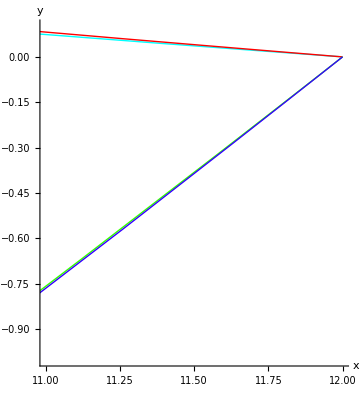

```mathematica
τend=.;uinvar = 0;
M=1;a=1;rplus=M+Sqrt[M^2-a^2];
horizpl=PolarPlot[rplus,{θ,0,2 Pi},DisplayFunction->Identity,PlotStyle->{Black,Thick}];
τPlot=1000;
(* first ray co rotates and escapes - blue
second ray co rotates and falls in - green
third ray counter rotates and escapes - red
fourth ray counter rotates and falls in - cyan *)
genXYPlot[τPlot,{0,12,π/2,0},{-0.15,0,0-0.0097},0.7];
genXYPlot[τPlot,{0,12,π/2,0},{-0.15,0,0-0.0096},0.3];
genXYPlot[τPlot,{0,12,π/2,0},{-0.15,0,0+0.0010},1];
genXYPlot[τPlot,{0,12,π/2,0},{-0.15,0,0+0.0009},1.5];
(*Manipulate[Show[horizpl,%,DisplayFunction->$DisplayFunction,AxesLabel->{x,y},PlotRange -> {{-coordMax,coordMax},{-coordMax,coordMax}}],{coordMax,2,10}]*)
Show[horizpl,%,%%,%%%,%%%%,DisplayFunction->$DisplayFunction,AxesLabel->{x,y},PlotRange -> {{11,12},{-1,0.1}}]
```

The particle did not cross the horizon for initial coordinates={0,12,π/2,0} and initial velocities={-0.15,0.001,-0.0103}

With final coordinates={t = 52.056,r = 21.5363,θ = 1.48188,ϕ = -3.94116}

For initial coordinates={0,12,π/2,0} and initial velocities={-0.15,0.001,-0.0048} the particle crosses the horizon at τend=74.5455

With final coordinates={t = 310.142,r = 1.005,θ = 3.13758,ϕ = 56.6528}

The particle did not cross the horizon for initial coordinates={0,12,π/2,0} and initial velocities={-0.15,0.001,0.0007}

With final coordinates={t = 50.3199,r = 13.914,θ = 1.41288,ϕ = 14.8021}

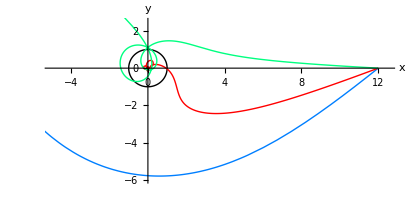

```mathematica
τend=.;uinvar = 0;
M=1;a=1;rplus=M+Sqrt[M^2-a^2];
horizpl=PolarPlot[rplus,{θ,0,2 Pi},DisplayFunction->Identity,PlotStyle->{Black,Thick}];
τPlot=200;
Table[genXYPlot[τPlot,{0,12,π/2,0},{-0.15,0.001,0+i*0.001},1-i*(5/6)],{i,-10.3,1.3,5.5}];
Show[horizpl,%,DisplayFunction->$DisplayFunction,AxesLabel->{x,y},PlotRange -> {{-5,12.5},{-6,2.5}}]
```

The particle did not cross the horizon for initial coordinates={0,12,π/2,0} and initial velocities={-0.15,0.001,-0.0096}

With final coordinates={t = 211.945,r = 157.78,θ = 1.66892,ϕ = -6.49428}

For initial coordinates={0,12,π/2,0} and initial velocities={-0.15,0.001,-0.0095} the particle crosses the horizon at τend=130.447

With final coordinates={t = 289.723,r = 1.005,θ = 3.1204,ϕ = 44.2011}

The particle did not cross the horizon for initial coordinates={0,12,π/2,0} and initial velocities={-0.15,0.001,0.0006}

With final coordinates={t = 178.344,r = 130.017,θ = 2.15338,ϕ = 23.8388}

For initial coordinates={0,12,π/2,0} and initial velocities={-0.15,0.001,0.0005} the particle crosses the horizon at τend=123.321

With final coordinates={t = 100.293,r = 1.005,θ = 0.0697766,ϕ = 108.826}

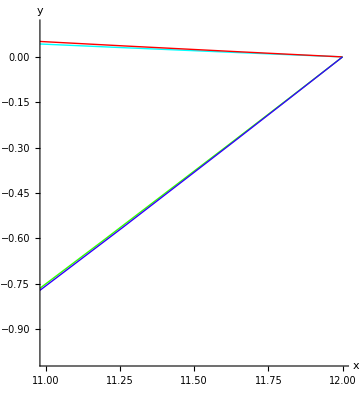

The particle did not cross the horizon for initial coordinates={0,12,π/2,0} and initial velocities={-0.15,0.001,-0.0096}

With final coordinates={t = 211.945,r = 157.78,θ = 1.66892,ϕ = -6.49428}

For initial coordinates={0,12,π/2,0} and initial velocities={-0.15,0.001,-0.0095} the particle crosses the horizon at τend=130.447

With final coordinates={t = 289.723,r = 1.005,θ = 3.1204,ϕ = 44.2011}

The particle did not cross the horizon for initial coordinates={0,12,π/2,0} and initial velocities={-0.15,0.001,0.0006}

With final coordinates={t = 178.344,r = 130.017,θ = 2.15338,ϕ = 23.8388}

For initial coordinates={0,12,π/2,0} and initial velocities={-0.15,0.001,0.0005} the particle crosses the horizon at τend=123.321

With final coordinates={t = 100.293,r = 1.005,θ = 0.0697766,ϕ = 108.826}

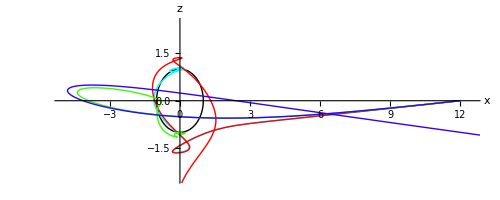

```mathematica
τend=.;uinvar = 0;
M=1;a=1;rplus=M+Sqrt[M^2-a^2];
horizpl=PolarPlot[rplus,{θ,0,2 Pi},DisplayFunction->Identity,PlotStyle->{Black,Thick}];
τPlot=1000;
(* first ray co rotates and escapes - blue
second ray co rotates and falls in - green
third ray counter rotates and escapes - red
fourth ray counter rotates and falls in - cyan *)
genXYPlot[τPlot,{0,12,π/2,0},{-0.15,0.001,0-0.0096},0.7];
genXYPlot[τPlot,{0,12,π/2,0},{-0.15,0.001,0-0.0095},0.3];
genXYPlot[τPlot,{0,12,π/2,0},{-0.15,0.001,0+0.0006},1];
genXYPlot[τPlot,{0,12,π/2,0},{-0.15,0.001,0+0.0005},1.5];
(*Manipulate[Show[horizpl,%,DisplayFunction->$DisplayFunction,AxesLabel->{x,y},PlotRange -> {{-coordMax,coordMax},{-coordMax,coordMax}}],{coordMax,2,10}]*)
Show[horizpl,%,%%,%%%,%%%%,DisplayFunction->$DisplayFunction,AxesLabel->{x,y},PlotRange -> {{11,12},{-1,0.1}}]
genXZPlot[τPlot,{0,12,π/2,0},{-0.15,0.001,0-0.0096},0.7];
genXZPlot[τPlot,{0,12,π/2,0},{-0.15,0.001,0-0.0095},0.3];
genXZPlot[τPlot,{0,12,π/2,0},{-0.15,0.001,0+0.0006},1];
genXZPlot[τPlot,{0,12,π/2,0},{-0.15,0.001,0+0.0005},1.5];
(*Manipulate[Show[horizpl,%,DisplayFunction->$DisplayFunction,AxesLabel->{x,y},PlotRange -> {{-coordMax,coordMax},{-coordMax,coordMax}}],{coordMax,2,10}]*)
Show[horizpl,%,%%,%%%,%%%%,DisplayFunction->$DisplayFunction,AxesLabel->{x,z},PlotRange -> {{-5,12.5},{-2.5,2.5}}]
```

The particle did not cross the horizon for initial coordinates={0,12,π/2,0} and initial velocities={-0.15,0,0.000971}

With final coordinates={t = 83.6375,r = 42.1444,θ = 1.5708,ϕ = 32.8632}

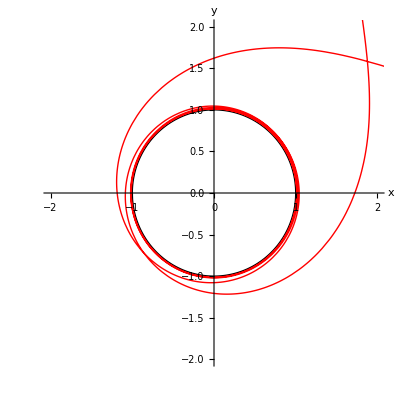

```mathematica
(* just for fun *)
τend=.;uinvar = 0;
M=1;a=1;rplus=M+Sqrt[M^2-a^2];
horizpl=PolarPlot[rplus,{θ,0,2 Pi},DisplayFunction->Identity,PlotStyle->{Black,Thick}];
τPlot=1000;
genXYPlot[τPlot,{0,12,π/2,0},{-0.15,0,0+0.000971},1];
Show[horizpl,%,DisplayFunction->$DisplayFunction,AxesLabel->{x,y},PlotRange -> {{-2,2},{-2,2}}]
```